```mathematica
SetOptions[$FrontEnd,"ClearEvaluationQueueOnKernelQuit"->False];Quit[];
```

# EWET FEYNCALC

```mathematica
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose = 0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr"}]];
```

Successfully patched FeynArts.

```mathematica
SetOptions[FourVector, FeynCalcInternal->False];
```

```mathematica
Model["EWET.fr"];
```

## Vertices checks

## H->PiPi Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,1->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3}],{S[1]}->{S[3],-S[3]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

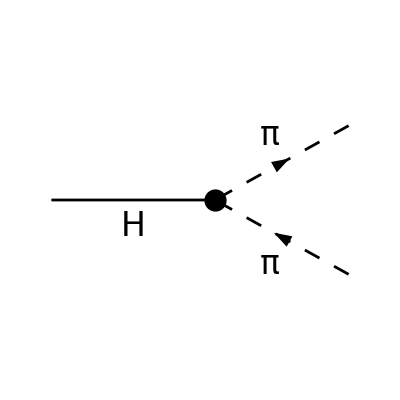

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1},
	OutgoingMomenta->{k1,k2},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]
```

-(2 a (OverBar[k1]·OverBar[k2]))/vev

## A->PiPi Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,1->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3}],{V[1]}->{S[3],-S[3]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

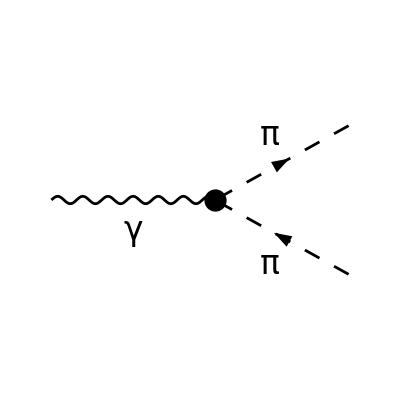

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1},
	OutgoingMomenta->{k1,k2},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]
```

-ⅈ ((4 ⅈ e F3n0 (OverBar[k2]·OverBar[p1]) (OverBar[k1]·ε̄(p1)))/vev^2-(4 ⅈ e F3n0 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·ε̄(p1)))/vev^2-ⅈ e (OverBar[k1]·ε̄(p1))+ⅈ e (OverBar[k2]·ε̄(p1)))

## Z->WW Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,1->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3}],{V[2]}->{V[3],-V[3]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

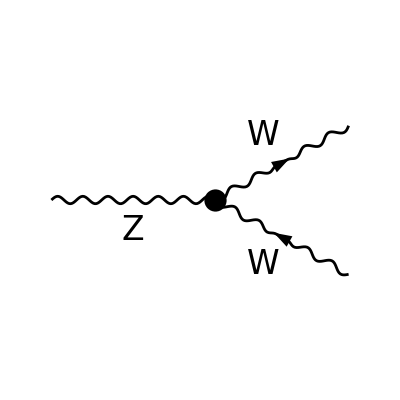

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1},
	OutgoingMomenta->{k1,k2},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]/.{SMP["e"]->g*sw}
```

-ⅈ (-(ⅈ g ((ε̄)^*(k1)·ε̄(p1)) (OverBar[p1]·(ε̄)^*(k2)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (2 F1n0-F3n0+FF1n0)))/(2 cw sw^2)+(ⅈ g (OverBar[p1]·(ε̄)^*(k1)) ((ε̄)^*(k2)·ε̄(p1)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (2 F1n0-F3n0+FF1n0)))/(2 cw sw^2)+(ⅈ g ((ε̄)^*(k1)·(ε̄)^*(k2)) (OverBar[k1]·ε̄(p1)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (F3n0+FF1n0)))/(2 cw sw^2)-(ⅈ g ((ε̄)^*(k1)·(ε̄)^*(k2)) (OverBar[k2]·ε̄(p1)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (F3n0+FF1n0)))/(2 cw sw^2)-(ⅈ g (OverBar[k1]·(ε̄)^*(k2)) ((ε̄)^*(k1)·ε̄(p1)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (F3n0+FF1n0)))/(2 cw sw^2)+(ⅈ g (OverBar[k2]·(ε̄)^*(k1)) ((ε̄)^*(k2)·ε̄(p1)) (cw^2 (g^2 sw^2 (-4 F2n0+F3n0+FF1n0-4 FF2n0)+2 sw^2)+g^2 sw^4 (F3n0+FF1n0)))/(2 cw sw^2))

## PiPi->Pi0Pi0 Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{4}],{S[3],-S[3]}->{S[2],S[2]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ,ExcludeParticles->{V[3]}];
```

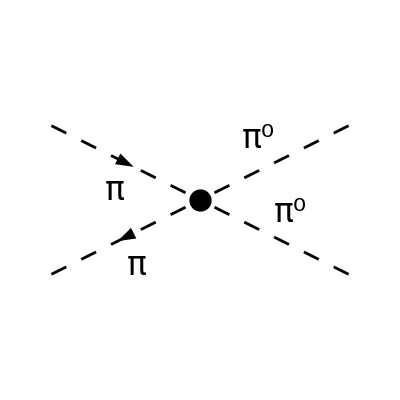

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]
```

-ⅈ ((2 ⅈ (OverBar[k1]·OverBar[k2]) (cw^2 vev^2+8 e^2 F10n0))/(3 cw^2 vev^4)+(ⅈ (OverBar[k1]·OverBar[p1]) (cw^2 vev^2+4 e^2 F10n0))/(3 cw^2 vev^4)+(ⅈ (OverBar[k1]·OverBar[p2]) (cw^2 vev^2+4 e^2 F10n0))/(3 cw^2 vev^4)+(ⅈ (OverBar[k2]·OverBar[p1]) (cw^2 vev^2+4 e^2 F10n0))/(3 cw^2 vev^4)+(ⅈ (OverBar[k2]·OverBar[p2]) (cw^2 vev^2+4 e^2 F10n0))/(3 cw^2 vev^4)+(16 ⅈ F4n0 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]))/vev^4+(16 ⅈ F4n0 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]))/vev^4+(32 ⅈ F5n0 (OverBar[k1]·OverBar[k2]) (OverBar[p1]·OverBar[p2]))/vev^4+(2 ⅈ (OverBar[p1]·OverBar[p2]))/(3 vev^2))

## WW->HH Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{4}],{V[3],-V[3]}->{S[1],S[1]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ,ExcludeParticles->{V[3]}];
```

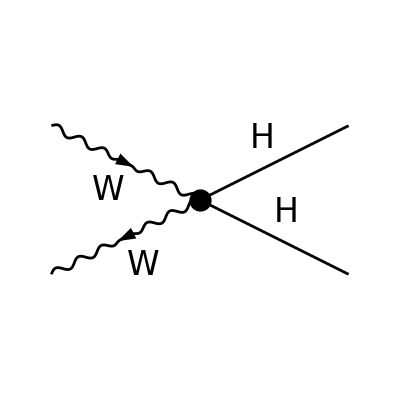

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]
```

-ⅈ ((ⅈ b e^2 (ε̄(p1)·ε̄(p2)))/(2 sw^2)+(4 ⅈ e^2 (F2n2+FF2n2) (OverBar[p1]·ε̄(p2)) (OverBar[p2]·ε̄(p1)))/(sw^2 vev^2)-(4 ⅈ e^2 (F2n2+FF2n2) (OverBar[p1]·OverBar[p2]) (ε̄(p1)·ε̄(p2)))/(sw^2 vev^2)-(2 ⅈ e^2 F6n0 (OverBar[k1]·OverBar[k2]) (ε̄(p1)·ε̄(p2)))/(sw^2 vev^2)-(ⅈ e^2 F7n0 (OverBar[k1]·ε̄(p2)) (OverBar[k2]·ε̄(p1)))/(sw^2 vev^2)-(ⅈ e^2 F7n0 (OverBar[k1]·ε̄(p1)) (OverBar[k2]·ε̄(p2)))/(sw^2 vev^2)+(ⅈ e^2 (F9n1+FF3n1) (OverBar[p1]·ε̄(p2)) (OverBar[k1]·ε̄(p1)+OverBar[k2]·ε̄(p1)))/(2 sw^2 vev^2)+(ⅈ e^2 (F9n1+FF3n1) (OverBar[p2]·ε̄(p1)) (OverBar[k1]·ε̄(p2)+OverBar[k2]·ε̄(p2)))/(2 sw^2 vev^2)-(ⅈ e^2 (F9n1+FF3n1) (ε̄(p1)·ε̄(p2)) (OverBar[k1]·OverBar[p1]+OverBar[k1]·OverBar[p2]+OverBar[k2]·OverBar[p1]+OverBar[k2]·OverBar[p2]))/(2 sw^2 vev^2))

## PiPi->AHH Vertex

```mathematica
diags=InsertFields[CreateTopologies[0,2->3,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{5}],{S[3],-S[3]}->{V[1],S[1],S[1]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ,ExcludeParticles->{V[3]}];
```

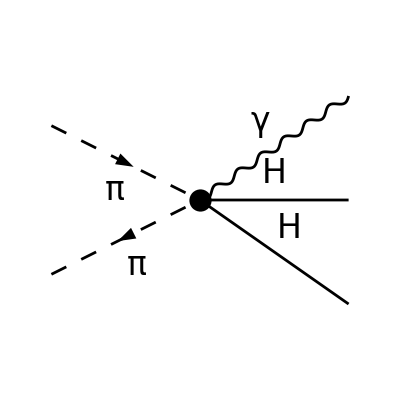

```mathematica
Paint[diags, ColumnsXRows -> {1, 1}, Numbering -> None,
	SheetHeader->None];
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},
	OutgoingMomenta->{k1,k2,k3},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]]/.{b->0,F6n0->0,F7n0->0,F9n1->0}
```

-ⅈ ((8 ⅈ e F3n2 (OverBar[k1]·OverBar[p2]) (OverBar[p1]·(ε̄)^*(k1)))/vev^4-(8 ⅈ e F3n2 (OverBar[k1]·OverBar[p1]) (OverBar[p2]·(ε̄)^*(k1)))/vev^4)

## Amplitudes Checks

## PiPi->Pi0Pi0 Amplitude

```mathematica
diags=InsertFields[CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3,4}],{S[3],-S[3]}->{S[2],S[2]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

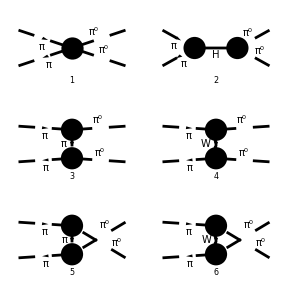

```mathematica
Paint[diags, ColumnsXRows -> {2, 3}, Numbering -> Simple,
	SheetHeader->Automatic];
```

```mathematica
ClearScalarProducts
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,0,0]
```

(0 | s/2 | -t/2 | -u/2 | 0 | -u/2 | -t/2 | 0 | s/2 | 0 | 0 | s/2 | -t/2 | -u/2 | 0 | -u/2 | -t/2 | 0 | s/2 | 0 | 0 | s/2 | -t/2 | -u/2 | 0 | -u/2 | -t/2 | 0 | s/2 | 0 | 0 | s/2 | -t/2 | -u/2 | 0 | -u/2 | -t/2 | 0 | s/2 | 0)

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//FeynAmpDenominatorExplicit]
```

-(a (a cw^2 vev^2+F10n1 e^2) s^2)/(cw^2 vev^4 (s-m_H^2))-(2 F10n0 e^2 ((F10n0 t e^2)/(cw^2 vev^3)+(2 F10n0 (-s/2-u/2) e^2)/(cw^2 vev^3)))/(cw^2 vev^3)-(2 F10n0 e^2 ((2 F10n0 (-s/2-t/2) e^2)/(cw^2 vev^3)+(F10n0 u e^2)/(cw^2 vev^3)))/(cw^2 vev^3)-ⅈ ((8 ⅈ F5n0 s^2)/vev^4+(ⅈ (cw^2 vev^2+8 F10n0 e^2) s)/(3 cw^2 vev^4)+(ⅈ s)/(3 vev^2)-(ⅈ t (cw^2 vev^2+4 F10n0 e^2))/(3 cw^2 vev^4)-(ⅈ u (cw^2 vev^2+4 F10n0 e^2))/(3 cw^2 vev^4)+(4 ⅈ F4n0 t^2)/vev^4+(4 ⅈ F4n0 u^2)/vev^4)-((ⅈ e (-vev^2 cw^2+2 F3n0 t cw^2+2 FF1n0 t cw^2-4 F10n0 e^2) (-(ⅈ u e)/(4 sw)+(ⅈ s (cw^2 vev^2+4 F10n0 e^2) e)/(4 cw^2 sw vev^2)+(ⅈ (F3n0+FF1n0) s (s/2+u/2) e)/(sw vev^2)+(ⅈ (F3n0+FF1n0) (-s/2-u/2) u e)/(sw vev^2)))/(2 cw^2 sw vev^2)+(ⅈ (-vev^2+2 F3n0 t+2 FF1n0 t) e (-(ⅈ u (cw^2 vev^2+4 F10n0 e^2) e)/(4 cw^2 sw vev^2)+(ⅈ s e)/(4 sw)-(ⅈ (F3n0+FF1n0) s (-s/2-u/2) e)/(sw vev^2)-(ⅈ (F3n0+FF1n0) (s/2+u/2) u e)/(sw vev^2)))/(2 sw vev^2))/(t-m_W^2)-((ⅈ e (-vev^2 cw^2+2 F3n0 u cw^2+2 FF1n0 u cw^2-4 F10n0 e^2) (-(ⅈ t e)/(4 sw)+(ⅈ s (cw^2 vev^2+4 F10n0 e^2) e)/(4 cw^2 sw vev^2)+(ⅈ (F3n0+FF1n0) s (s/2+t/2) e)/(sw vev^2)+(ⅈ (F3n0+FF1n0) (-s/2-t/2) t e)/(sw vev^2)))/(2 cw^2 sw vev^2)+(ⅈ (-vev^2+2 F3n0 u+2 FF1n0 u) e (-(ⅈ t (cw^2 vev^2+4 F10n0 e^2) e)/(4 cw^2 sw vev^2)+(ⅈ s e)/(4 sw)-(ⅈ (F3n0+FF1n0) s (-s/2-t/2) e)/(sw vev^2)-(ⅈ (F3n0+FF1n0) (s/2+t/2) t e)/(sw vev^2)))/(2 sw vev^2))/(u-m_W^2)

```mathematica
simp=Simplify[M]
```

1/(24 cw^4 vev^6)(-(24 a cw^2 s^2 vev^2 (a cw^2 vev^2+e^2 F10n1))/(s-m_H^2)+8 cw^2 vev^2 (cw^2 (12 F4n0 (t^2+u^2)+24 F5n0 s^2+vev^2 (2 s-t-u))+4 e^2 F10n0 (2 s-t-u))-(6 e^2 vev^2 (-(cw^4 (s-u) (2 F3n0 t+2 FF1n0 t-vev^2) (2 F3n0 (s+u)+2 FF1n0 (s+u)+vev^2))+4 cw^2 e^2 F10n0 (s-u) (F3n0 (s-t+u)+FF1n0 (s-t+u)+vev^2)+8 e^4 F10n0^2 s))/(sw^2 (t-m_W^2))-(6 e^2 vev^2 (-(cw^4 (s-t) (2 F3n0 u+2 FF1n0 u-vev^2) (2 F3n0 (s+t)+2 FF1n0 (s+t)+vev^2))+4 cw^2 e^2 F10n0 (s-t) (F3n0 (s+t-u)+FF1n0 (s+t-u)+vev^2)+8 e^4 F10n0^2 s))/(sw^2 (u-m_W^2))+48 e^4 F10n0^2 (s+t-u)+48 e^4 F10n0^2 (s-t+u))

## PiPi->HH Amplitude

```mathematica
diags=InsertFields[CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3,4}],{S[3],-S[3]}->{S[1],S[1]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

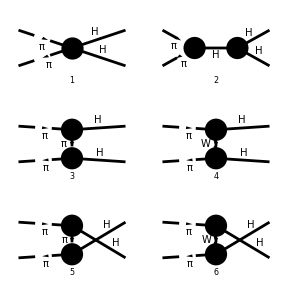

```mathematica
Paint[diags, ColumnsXRows -> {2, 3}, Numbering -> Simple,
	SheetHeader->Automatic];
```

```mathematica
ClearScalarProducts
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,SMP["m_H"],SMP["m_H"]]
```

(m_H^2 | s/2-m_H^2 | m_H^2/2-t/2 | m_H^2/2-u/2 | m_H^2 | m_H^2/2-u/2 | m_H^2/2-t/2 | 0 | s/2 | 0 | m_H^2 | s/2-m_H^2 | m_H^2/2-t/2 | m_H^2/2-u/2 | m_H^2 | m_H^2/2-u/2 | m_H^2/2-t/2 | 0 | s/2 | 0 | m_H^2 | s/2-m_H^2 | m_H^2/2-t/2 | m_H^2/2-u/2 | m_H^2 | m_H^2/2-u/2 | m_H^2/2-t/2 | 0 | s/2 | 0 | m_H^2 | s/2-m_H^2 | m_H^2/2-t/2 | m_H^2/2-u/2 | m_H^2 | m_H^2/2-u/2 | m_H^2/2-t/2 | 0 | s/2 | 0)

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//FeynAmpDenominatorExplicit]
```

-(4 a^2 (m_H^2/2-t/2) (-m_H^2/2+s/2+u/2))/(t vev^2)-(4 a^2 (m_H^2/2-u/2) (-m_H^2/2+s/2+t/2))/(u vev^2)-(3 a b3 s m_H^2)/(vev^2 (s-m_H^2))-((e (2 a vev^2-F9n0 m_H^2-F9n0 t-FF3n0 m_H^2-FF3n0 t) ((a e s)/(2 sw)+(e (F9n0+FF3n0) (m_H^2/2-u/2) (-m_H^2/2+s/2+u/2))/(sw vev^2)-(e s (F9n0+FF3n0) ((3 m_H^2)/2-s/2-u/2))/(2 sw vev^2)))/(2 sw vev^2)-(e (F9n0+FF3n0) (t-m_H^2) ((a e (m_H^2/2-u/2))/sw+(e (F9n0+FF3n0) (s/2-m_H^2) (-m_H^2/2+s/2+u/2))/(sw vev^2)-(e (F9n0+FF3n0) (m_H^2/2-u/2) ((3 m_H^2)/2-s/2-u/2))/(sw vev^2)))/(2 sw vev^2))/(t-m_W^2)-((e (2 a vev^2-F9n0 m_H^2-F9n0 u-FF3n0 m_H^2-FF3n0 u) ((a e s)/(2 sw)+(e (F9n0+FF3n0) (m_H^2/2-t/2) (-m_H^2/2+s/2+t/2))/(sw vev^2)-(e s (F9n0+FF3n0) ((3 m_H^2)/2-s/2-t/2))/(2 sw vev^2)))/(2 sw vev^2)-(e (F9n0+FF3n0) (u-m_H^2) ((a e (m_H^2/2-t/2))/sw+(e (F9n0+FF3n0) (s/2-m_H^2) (-m_H^2/2+s/2+t/2))/(sw vev^2)-(e (F9n0+FF3n0) (m_H^2/2-t/2) ((3 m_H^2)/2-s/2-t/2))/(sw vev^2)))/(2 sw vev^2))/(u-m_W^2)-ⅈ (-(ⅈ b s)/vev^2+(4 ⅈ F6n0 s (s/2-m_H^2))/vev^4+(4 ⅈ F7n0 (m_H^2/2-t/2)^2)/vev^4+(4 ⅈ F7n0 (m_H^2/2-u/2)^2)/vev^4)

```mathematica
simp=Simplify[M]
```

-1/(4 vev^4)(1/(sw^2 (u-m_W^2))e^2 (2 a^2 s vev^4+(F9n0+FF3n0) m_H^2 (a vev^2 (-3 s+t-u)+2 F9n0 u (s-t)+2 FF3n0 u (s-t))-F9n0 (s-t) (2 FF3n0 u (s+t)-a vev^2 (s+t-u))+a FF3n0 s^2 vev^2-a FF3n0 s u vev^2-a FF3n0 t^2 vev^2+a FF3n0 t u vev^2+F9n0^2 u (t^2-s^2)+u (F9n0+FF3n0)^2 m_H^4-FF3n0^2 s^2 u+FF3n0^2 t^2 u)+1/(sw^2 (t-m_W^2))e^2 (2 a^2 s vev^4+(F9n0+FF3n0) m_H^2 (a vev^2 (-3 s-t+u)+2 F9n0 t (s-u)+2 FF3n0 t (s-u))-F9n0 (s-u) (2 FF3n0 t (s+u)-a vev^2 (s-t+u))+a FF3n0 s^2 vev^2-a FF3n0 s t vev^2+a FF3n0 t u vev^2-a FF3n0 u^2 vev^2+F9n0^2 t (u^2-s^2)+t (F9n0+FF3n0)^2 m_H^4-FF3n0^2 s^2 t+FF3n0^2 t u^2)-(4 a^2 vev^2 (u-m_H^2) (-m_H^2+s+t))/u-(4 a^2 vev^2 (t-m_H^2) (-m_H^2+s+u))/t+(12 a b3 s vev^2 m_H^2)/(s-m_H^2)-4 (-b s vev^2-2 m_H^2 (2 F6n0 s+F7n0 (t+u))+2 F6n0 s^2+2 F7n0 m_H^4+F7n0 t^2+F7n0 u^2))

## HH->HH Amplitude

```mathematica
diags=InsertFields[CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections(*,Internal, Reducible*)},Adjacencies->{3,4}],{S[1],S[1]}->{S[1],S[1]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

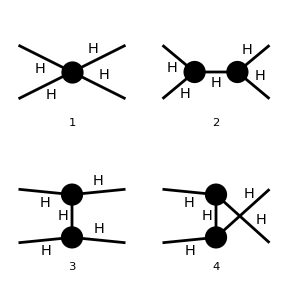

```mathematica
Paint[diags, ColumnsXRows -> {2, 2}, Numbering -> Simple,
	SheetHeader->Automatic];
```

```mathematica
ClearScalarProducts
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_H"],SMP["m_H"],SMP["m_H"],SMP["m_H"]]
```

(m_H^2 | s/2-m_H^2 | m_H^2-t/2 | m_H^2-u/2 | m_H^2 | m_H^2-u/2 | m_H^2-t/2 | m_H^2 | s/2-m_H^2 | m_H^2 | m_H^2 | s/2-m_H^2 | m_H^2-t/2 | m_H^2-u/2 | m_H^2 | m_H^2-u/2 | m_H^2-t/2 | m_H^2 | s/2-m_H^2 | m_H^2 | m_H^2 | s/2-m_H^2 | m_H^2-t/2 | m_H^2-u/2 | m_H^2 | m_H^2-u/2 | m_H^2-t/2 | m_H^2 | s/2-m_H^2 | m_H^2 | m_H^2 | s/2-m_H^2 | m_H^2-t/2 | m_H^2-u/2 | m_H^2 | m_H^2-u/2 | m_H^2-t/2 | m_H^2 | s/2-m_H^2 | m_H^2)

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//FeynAmpDenominatorExplicit]
```

-(9 b3^2 m_H^4)/(vev^2 (s-m_H^2))-(9 b3^2 m_H^4)/(vev^2 (t-m_H^2))-(9 b3^2 m_H^4)/(vev^2 (u-m_H^2))-ⅈ (-(12 ⅈ b4 m_H^2)/vev^2+(8 ⅈ F8n0 (s/2-m_H^2)^2)/vev^4+(8 ⅈ F8n0 (m_H^2-t/2)^2)/vev^4+(8 ⅈ F8n0 (m_H^2-u/2)^2)/vev^4)

## H->APi0 y AZ New Amplitude

## Tree level

```mathematica
diags=InsertFields[CreateTopologies[0,1->2,Adjacencies->{3,4,5,6}(*,ExcludeTopologies->{Tadpoles, WFCorrections,Internal, Reducible}*)],{S[1]}->{V[1],S[2]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

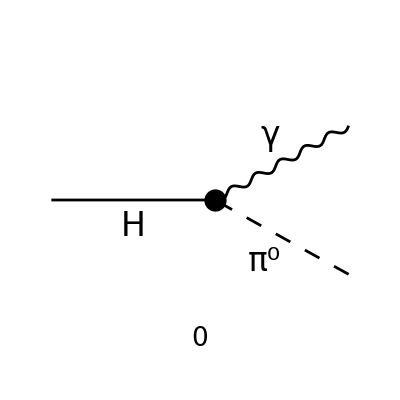

FeynArtsGraphics()(([1]))

```mathematica
Paint[diags, ColumnsXRows -> {1,1}, Numbering -> Simple,
	SheetHeader->None]
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//FeynAmpDenominatorExplicit]/.{F6n0->0,F7n0->0,F10n3->0}
```

-ⅈ ((2 e FF3n0 (m_H^2-t/2) (OverBar[k2]·(ε̄)^*(k1)))/vev^2-(2 e FF3n0 (s/2-m_H^2) (OverBar[p1]·(ε̄)^*(k1)))/vev^2)

## One loop

```mathematica
diags=InsertFields[CreateTopologies[1,1->2,Adjacencies->{3,4,5,6}(*,ExcludeTopologies->{Tadpoles, WFCorrections,Internal, Reducible}*)],{S[1]}->{V[1],S[2]},Model->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"SixPartVertsLagr/SixPartVertsLagr"}],InsertionLevel->{Classes} ];
```

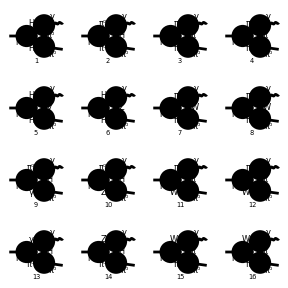

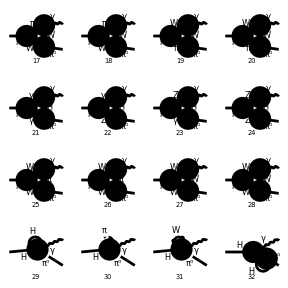

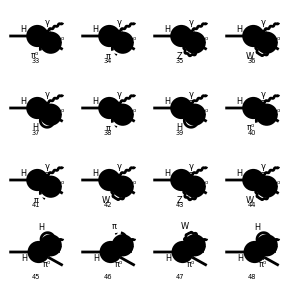

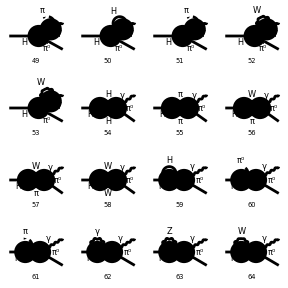

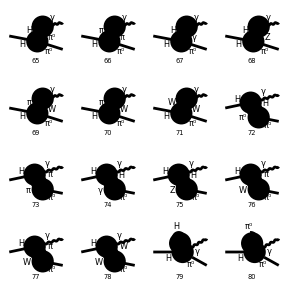

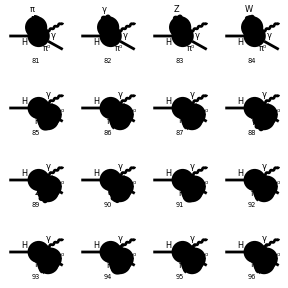

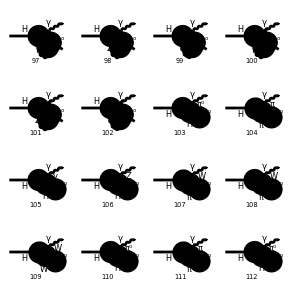

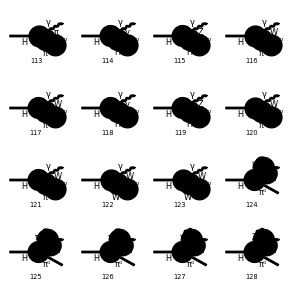

FeynArtsGraphics()(([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8]
[9] | [10] | [11] | [12]
[13] | [14] | [15] | [16]),([17] | [18] | [19] | [20]
[21] | [22] | [23] | [24]
[25] | [26] | [27] | [28]
[29] | [30] | [31] | [32]),([33] | [34] | [35] | [36]
[37] | [38] | [39] | [40]
[41] | [42] | [43] | [44]
[45] | [46] | [47] | [48]),([49] | [50] | [51] | [52]
[53] | [54] | [55] | [56]
[57] | [58] | [59] | [60]
[61] | [62] | [63] | [64]),([65] | [66] | [67] | [68]
[69] | [70] | [71] | [72]
[73] | [74] | [75] | [76]
[77] | [78] | [79] | [80]),([81] | [82] | [83] | [84]
[85] | [86] | [87] | [88]
[89] | [90] | [91] | [92]
[93] | [94] | [95] | [96]),([97] | [98] | [99] | [100]
[101] | [102] | [103] | [104]
[105] | [106] | [107] | [108]
[109] | [110] | [111] | [112]),([113] | [114] | [115] | [116]
[117] | [118] | [119] | [120]
[121] | [122] | [123] | [124]
[125] | [126] | [127] | [128]),([129] | [130] | [131] | [132]
[133] | [134] | [135] | [136]
[137] | [138] | [139] | [140]
[141] | [142] | [143] | [144]),([145] | [146] | [147] | [148]
[149] | [150] | [151] | [152]
[153] | [154] | [155] | [156]
[157] | [158] | [159] | [160]),([161] | [162] | [163] | [164]
[165] | [166] | [167] | [168]
[169] | [170] | [171] | [172]
[173] | [174] | [175] | [176]),([177] | [178] | [179] | Null
Null | Null | Null | Null
Null | Null | Null | Null
Null | Null | Null | Null))

```mathematica
Paint[diags, ColumnsXRows -> {4,4}, Numbering -> Simple,
	SheetHeader->None]
```

```mathematica
M=ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False, ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//FeynAmpDenominatorExplicit]/.{F6n0->0,F7n0->0,F10n3->0}
```

(9 b3^2 ((FF3n0 s (OverBar[k2]·(ε̄)^*(k1)) e)/vev^2-(2 FF3n0 (OverBar[k1]·(ε̄)^*(k1)+OverBar[k2]·(ε̄)^*(k1)) e (s/2-m_H^2))/vev^2) m_H^4)/(32 π^4 vev^2 (s-m_H^2) (OverBar[LoopMom1]^2-m_H^2) (-m_H^2+s-2 (OverBar[k1]·OverBar[LoopMom1])-2 (OverBar[k2]·OverBar[LoopMom1])+OverBar[LoopMom1]^2))+245+((1/sw^2+1/1)1(11)/(16 π^4 (1^2-m_W^2) m_H^4)+(((6 ⅈ ((F2n1+FF2n1) cw^4-F1n1 sw^2 cw^2+(2 F11n1+F2n1-FF2n1) sw^4) OverBar[LoopMom1]^2 e^2)/(cw^2 sw^2 vev)+(2 ⅈ (1)^2 (a cw^2 vev^2+F10n1 e^2) e^2)/(cw^4 sw^2 vev)) (-(FF3n0 3)/vev^2-(FF3n0 e 1 (1))/vev^2))/(32 π^4 (OverBar[LoopMom1]^2-m_Z^2) m_H^4)
 |  |  |  |